```mathematica
ClearAll["Global`*"]
```

```mathematica
(* Gaussian sensing: Kitaev chain*)

(*a1,a2,...,an,a1d,...and -> x1,x2...,xn,p1,...pn*)
QT[N1_]:=Module[{i,j,Matrix},
Matrix=0*IdentityMatrix[2*N1];
For[i=1,i<=N1,i++,
Matrix[[i,i]]=1;
Matrix[[i,N1+i]]=1;
Matrix[[i+N1,i]]=-ⅈ;
Matrix[[i+N1,N1+i]]=ⅈ;
];
Matrix/√2
]

AMatrix[N1_,g_,ϕb_]:=Module[{A,i,j},
A=ConstantArray[0,{N1,N1}];
For[i=1,i<=N1,i++,
For[j=1,j<=N1,j++,
If[i!=j && Abs[i-j]==1,
If[i<j,A[[i,j]]=g*Exp[-ⅈ*ϕb],
A[[i,j]]=-g*Exp[ⅈ*ϕb]
];
];
]
];
A
]

BMatrix[N1_,g_,ϕb_,χ_,ϕχ_, m_]:=Module[{A,i,j},
A=ConstantArray[0,{N1,N1}];
For[i=1,i<=N1,i++,
For[j=1,j<=N1,j++,
If[ Abs[i-j]==1,
If[i<j,If[m!={}&&IntersectingQ[{i},m], A[[i,j]]=g*Exp[-ⅈ*ϕb],A[[i,j]]=χ*Exp[-ⅈ*ϕχ]]];
If[i>j,If[m!={}&&IntersectingQ[{i},m], A[[i,j]]=g*Exp[-ⅈ*ϕb],A[[i,j]]=χ*Exp[-ⅈ*ϕχ]]];
];
];
];
A
]


BosonicKitaevChain[N1_,g_,ϕb_,χ_,ϕχ_,m_]:=Module[{},
A=AMatrix[N1,g,ϕb];
B=BMatrix[N1,g,ϕb,χ,ϕχ, m];
m1=Join[A,B,2];
m2=Join[Conjugate[B],Conjugate[A],2];
assump=g>=0&&χ>=0&&ϕb∈Reals&&ϕχ∈Reals;
$Assumptions=assump;
Simplify[Join[m1,m2]]
]

CovarBasis[N1_]:= Module[{i,j,A},
A=0*IdentityMatrix[2*N1];
For[i=1,i<=N1,i++,
A[[2i-1,i]]=1;
A[[2i,N1+i]]=1
];
A]



QFIperPhotonEP[Nmodes_]:=Module[{EOM,DM,S,Scovar,Σin,G,Sphase,Σout,λ,ϕ},
EOM=BosonicKitaevChain[Nmodes,χ,ϕb=0,χ,ϕχ=0,{}];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{1/4 Tr[Inverse[Σout].D[Σout,ϕ].Inverse[Σout].D[Σout,ϕ]/.ϕ->0]//FullSimplify,2 D[λ,ϕ].Inverse[Σout/.ϕ->0].D[λ,ϕ]/.ϕ->0//FullSimplify,1/4 (Tr[Σout]-2 Nmodes)+1/2 Transpose[λ].λ//FullSimplify}
]


QFIperPhotonEPAnal[Nmodes_]:=Module[{EOM,DM,S,Scovar,Σin,G,Sphase,Σout,λ,ϕ},
EOM=BosonicKitaevChain[Nmodes,χ,ϕb=0,χ,ϕχ=0,{}];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t]//FullSimplify;
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]]//FullSimplify;
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar]//FullSimplify;
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase]//FullSimplify;
λ=Sphase.Scovar.Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
{1/2 Tr[-Inverse[Σin].G.Σin.G/.ϕ->0]-Nmodes//FullSimplify,2 D[λ,ϕ].Inverse[Σout/.ϕ->0].D[λ,ϕ]/.ϕ->0//FullSimplify,1/4 (Tr[Σout]-2 Nmodes)+1/2 Transpose[λ].λ//FullSimplify}
]

QFInoDisp[Nmodes_,g_,χ_]:=Module[{EOM,DM,S,Scovar,Σin,G,Sphase,Σout,λ,ϕ},
EOM=BosonicKitaevChain[Nmodes,g,ϕb=0,χ,ϕχ=0,{}];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t];
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]];
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar];
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase];
(1/2 Tr[-Inverse[Σin].G.Σin.G/.ϕ->0]-Nmodes)/(1/4 (Tr[Σout]-2 Nmodes))//FullSimplify
]


LeadingOrderCheck[cov_,disp_,n_,Nmodes_]:=Module[{M,d,G,EOM,DM,DMq,CovForm,DispForm,nForm},
M=Nmodes;
d=Flatten@Table[{Symbol["x"<>ToString[i]],Symbol["p"<>ToString[i]]},{i,Nmodes}];
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
EOM=BosonicKitaevChain[Nmodes,χ,ϕb=0,χ,ϕχ=0,{}]//FullSimplify;
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
DMq=CovarBasis[Nmodes].DM.Transpose[CovarBasis[Nmodes]];

CovForm=Tr[1/2 1/((M-1)!)^4 MatrixPower[DMq,M-1].G.MatrixPower[DMq,M-1].MatrixPower[Transpose[DMq],M-1].Transpose[G].MatrixPower[Transpose[DMq],M-1]]//FullSimplify;
Print["leading order covariant ",CovForm];
Print[Coefficient[cov,t^(4M-4)]==CovForm//FullSimplify];

DispForm=(2 1)/((M-1)!)^4 d.MatrixPower[Transpose[DMq],M-1].Transpose[G].MatrixPower[Transpose[DMq],M-1].MatrixPower[DMq,M-1].G.MatrixPower[DMq,M-1].d//FullSimplify;
Print["leading order displacement ",DispForm];
Print[Coefficient[disp,t^(4M-4)]==DispForm//FullSimplify];

nForm=1/(2 ((M-1)!)^2)(Tr[MatrixPower[DMq,M-1].MatrixPower[Transpose[DMq],M-1]]+d.MatrixPower[Transpose[DMq],M-1].MatrixPower[DMq,M-1].d)//FullSimplify;
Print["leading order mean photon number  ",nForm];
Print[Coefficient[n,t^(2M-2)]==nForm//FullSimplify];
]


FnNormal[Nmodes_,g_,χ_,t_]:=Module[{},
λ=Table[2 Sqrt[χ^2-g^2] Cos[(k π)/(Nmodes+1)],{k,1,Nmodes}];
x=Table[((χ-g)/(χ+g))^(k/2) Sin[(h k π)/(Nmodes+1)]//Simplify,{k,1,Nmodes},{h,1,Nmodes}];
y=Table[((χ+g)/(χ-g))^(k/2) Sin[(h k π)/(Nmodes+1)]//Simplify,{h,1,Nmodes},{k,1,Nmodes}];
tr=Tr[(2/(Nmodes+1))^4 ArrayFlatten[ReleaseHold@DiagonalMatrix[Hold/@{-Transpose[y].MatrixExp[-DiagonalMatrix[λ]t].Transpose[x].x.MatrixExp[-DiagonalMatrix[λ]t].y.Transpose[y].MatrixExp[-DiagonalMatrix[λ ] t].Transpose[x].x.MatrixExp[-DiagonalMatrix[λ ] t].y,-x.MatrixExp[DiagonalMatrix[λ ] t].y.Transpose[y].MatrixExp[DiagonalMatrix[λ ] t].Transpose[x].x.MatrixExp[DiagonalMatrix[λ]t].y.Transpose[y].MatrixExp[DiagonalMatrix[λ]t].Transpose[x]}]]]//N;

nout=1/4 Tr[(2/(Nmodes+1))^2 ArrayFlatten[ReleaseHold@DiagonalMatrix[Hold/@{x.MatrixExp[-DiagonalMatrix[λ]t].y.Transpose[y].MatrixExp[-DiagonalMatrix[λ ] t].Transpose[x],x.MatrixExp[DiagonalMatrix[λ ] t].y.Transpose[y].MatrixExp[DiagonalMatrix[λ ] t].Transpose[x]}]]]-Nmodes/2//N;

Fcov=-1/2 tr-Nmodes;
Fcov/nout
]
```

```mathematica
(* single mode *)
({{-ⅈ Subscript[ω, 1], Subscript[ξ, 1]}, {Subscript[ξ, 1], ⅈ Subscript[ω, 1]}})//Eigenvalues/.Subscript[ω, 1]->0

Clear[ξ,ω]
Subscript[ξ, 1]=ξ;
Subscript[ω, 1]=ω;
Nmodes=1;
EOM=({{-ⅈ Subscript[ω, 1], Subscript[ξ, 1]}, {Subscript[ξ, 1], ⅈ Subscript[ω, 1]}});
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t];
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]];
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar];
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase];
1/4 Tr[Inverse[Σout].D[Σout,ϕ].Inverse[Σout].D[Σout,ϕ]/.ϕ->0]//FullSimplify
1/4 (Tr[Σout]-2 Nmodes)//FullSimplify
(1/4 Tr[Inverse[Σout].D[Σout,ϕ].Inverse[Σout].D[Σout,ϕ]/.ϕ->0])/(1/4 (Tr[Σout]-2 Nmodes))//FullSimplify
%/.ω->0//FullSimplify
```

{-√(ξ^2-ω^2),√(ξ^2-ω^2)}

(4 ξ^2 (ξ^2-2 ω^2+ξ^2 Cosh[2 t √((ξ-ω) (ξ+ω))]) Sinh[t √(ξ^2-ω^2)]^2)/((ξ^2-ω^2)^2)

(ξ^2 Sinh[t √(ξ^2-ω^2)]^2)/(ξ^2-ω^2)

(4 (ξ^2-2 ω^2+ξ^2 Cosh[2 t √(ξ^2-ω^2)]))/(ξ^2-ω^2)

8 Cosh[t ξ]^2

(0 | g | ξ1 | 0
-g | 0 | 0 | ξ2
ξ1 | 0 | 0 | g
0 | ξ2 | -g | 0)

(2 ⅇ^(2 t (ξ1+ξ2)) (-4 ⅇ^(-4 t (ξ1+ξ2)) (-4 g^2+(ξ1-ξ2)^2)^2+16 ⅇ^(-6 t (ξ1+ξ2)) g^2 (2 g^2+(ξ1-ξ2)^2)+16 ⅇ^(-2 t (ξ1+ξ2)) g^2 (2 g^2+(ξ1-ξ2)^2)-16 ⅇ^(-t (2 ξ1+√(-4 g^2+(ξ1-ξ2)^2)+2 ξ2)) g^2 (ξ1-ξ2)^2-16 ⅇ^(-t (6 ξ1+√(-4 g^2+(ξ1-ξ2)^2)+6 ξ2)) g^2 (ξ1-ξ2)^2-16 ⅇ^(t (√(-4 g^2+(ξ1-ξ2)^2)-6 (ξ1+ξ2))) g^2 (ξ1-ξ2)^2-16 ⅇ^(t (√(-4 g^2+(ξ1-ξ2)^2)-2 (ξ1+ξ2))) g^2 (ξ1-ξ2)^2+ⅇ^(-2 t (ξ1-√(-4 g^2+(ξ1-ξ2)^2)+ξ2)) (ξ1-ξ2)^4+ⅇ^(-2 t (ξ1+√(-4 g^2+(ξ1-ξ2)^2)+ξ2)) (ξ1-ξ2)^4+ⅇ^(-2 t (3 ξ1+√(-4 g^2+(ξ1-ξ2)^2)+3 ξ2)) (ξ1-ξ2)^4+ⅇ^(2 t (√(-4 g^2+(ξ1-ξ2)^2)-3 (ξ1+ξ2))) (ξ1-ξ2)^4))/((-4 g^2+(ξ1-ξ2)^2) (-8 ⅇ^(-3 t (ξ1+ξ2)) g^2-8 ⅇ^(-t (ξ1+ξ2)) g^2-4 ⅇ^(-2 t (ξ1+ξ2)) (-4 g^2+(ξ1-ξ2)^2)+ⅇ^(-t (ξ1+√(-4 g^2+(ξ1-ξ2)^2)+ξ2)) (ξ1-ξ2)^2+ⅇ^(-t (3 ξ1+√(-4 g^2+(ξ1-ξ2)^2)+3 ξ2)) (ξ1-ξ2)^2+ⅇ^(t (√(-4 g^2+(ξ1-ξ2)^2)-3 (ξ1+ξ2))) (ξ1-ξ2)^2+ⅇ^(t √(-4 g^2+(ξ1-ξ2)^2)-t (ξ1+ξ2)) (ξ1-ξ2)^2))

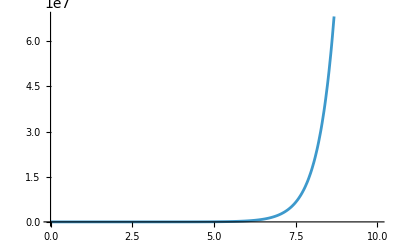

```mathematica
(* two single modes *)

Clear[ξ1,ξ2,ω,g]
Nmodes=2;
EOM={{0,g,ξ1,0},{-g,0,0,ξ2},{ξ1,0,0,g},{0,ξ2,-g,0}};
EOM//MatrixForm
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t];
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]];
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar];
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];

(1/2 Tr[-Inverse[Σin].G.Σin.G/.ϕ->0]-Nmodes)/(1/4 (Tr[Σin]-2 Nmodes))//FullSimplify
Plot[%/.ξ1->1/.ξ2->1,{t,0,10}]
```

```mathematica
"2 SMSV + BS"
Clear[g,ξ1,ξ2]
TSMSVBS=(2 ⅇ^(2 t (ξ1+ξ2)) (-4 ⅇ^(-4 t (ξ1+ξ2)) (-4 g^2+(ξ1-ξ2)^2)^2+16 ⅇ^(-6 t (ξ1+ξ2)) g^2 (2 g^2+(ξ1-ξ2)^2)+16 ⅇ^(-2 t (ξ1+ξ2)) g^2 (2 g^2+(ξ1-ξ2)^2)-16 ⅇ^(-t (2 ξ1+√(-4 g^2+(ξ1-ξ2)^2)+2 ξ2)) g^2 (ξ1-ξ2)^2-16 ⅇ^(-t (6 ξ1+√(-4 g^2+(ξ1-ξ2)^2)+6 ξ2)) g^2 (ξ1-ξ2)^2-16 ⅇ^(t (√(-4 g^2+(ξ1-ξ2)^2)-6 (ξ1+ξ2))) g^2 (ξ1-ξ2)^2-16 ⅇ^(t (√(-4 g^2+(ξ1-ξ2)^2)-2 (ξ1+ξ2))) g^2 (ξ1-ξ2)^2+ⅇ^(-2 t (ξ1-√(-4 g^2+(ξ1-ξ2)^2)+ξ2)) (ξ1-ξ2)^4+ⅇ^(-2 t (ξ1+√(-4 g^2+(ξ1-ξ2)^2)+ξ2)) (ξ1-ξ2)^4+ⅇ^(-2 t (3 ξ1+√(-4 g^2+(ξ1-ξ2)^2)+3 ξ2)) (ξ1-ξ2)^4+ⅇ^(2 t (√(-4 g^2+(ξ1-ξ2)^2)-3 (ξ1+ξ2))) (ξ1-ξ2)^4))/((-4 g^2+(ξ1-ξ2)^2) (-8 ⅇ^(-3 t (ξ1+ξ2)) g^2-8 ⅇ^(-t (ξ1+ξ2)) g^2-4 ⅇ^(-2 t (ξ1+ξ2)) (-4 g^2+(ξ1-ξ2)^2)+ⅇ^(-t (ξ1+√(-4 g^2+(ξ1-ξ2)^2)+ξ2)) (ξ1-ξ2)^2+ⅇ^(-t (3 ξ1+√(-4 g^2+(ξ1-ξ2)^2)+3 ξ2)) (ξ1-ξ2)^2+ⅇ^(t (√(-4 g^2+(ξ1-ξ2)^2)-3 (ξ1+ξ2))) (ξ1-ξ2)^2+ⅇ^(t √(-4 g^2+(ξ1-ξ2)^2)-t (ξ1+ξ2)) (ξ1-ξ2)^2))//FullSimplify
```

2 SMSV + BS

(2 ⅇ^(2 t (ξ1+ξ2)) (-4 ⅇ^(-4 t (ξ1+ξ2)) (-4 g^2+(ξ1-ξ2)^2)^2+16 ⅇ^(-6 t (ξ1+ξ2)) g^2 (2 g^2+(ξ1-ξ2)^2)+16 ⅇ^(-2 t (ξ1+ξ2)) g^2 (2 g^2+(ξ1-ξ2)^2)-16 ⅇ^(-t (2 ξ1+√(-4 g^2+(ξ1-ξ2)^2)+2 ξ2)) g^2 (ξ1-ξ2)^2-16 ⅇ^(-t (6 ξ1+√(-4 g^2+(ξ1-ξ2)^2)+6 ξ2)) g^2 (ξ1-ξ2)^2-16 ⅇ^(t (√(-4 g^2+(ξ1-ξ2)^2)-6 (ξ1+ξ2))) g^2 (ξ1-ξ2)^2-16 ⅇ^(t (√(-4 g^2+(ξ1-ξ2)^2)-2 (ξ1+ξ2))) g^2 (ξ1-ξ2)^2+ⅇ^(-2 t (ξ1-√(-4 g^2+(ξ1-ξ2)^2)+ξ2)) (ξ1-ξ2)^4+ⅇ^(-2 t (ξ1+√(-4 g^2+(ξ1-ξ2)^2)+ξ2)) (ξ1-ξ2)^4+ⅇ^(-2 t (3 ξ1+√(-4 g^2+(ξ1-ξ2)^2)+3 ξ2)) (ξ1-ξ2)^4+ⅇ^(2 t (√(-4 g^2+(ξ1-ξ2)^2)-3 (ξ1+ξ2))) (ξ1-ξ2)^4))/((-4 g^2+(ξ1-ξ2)^2) (-8 ⅇ^(-3 t (ξ1+ξ2)) g^2-8 ⅇ^(-t (ξ1+ξ2)) g^2-4 ⅇ^(-2 t (ξ1+ξ2)) (-4 g^2+(ξ1-ξ2)^2)+ⅇ^(-t (ξ1+√(-4 g^2+(ξ1-ξ2)^2)+ξ2)) (ξ1-ξ2)^2+ⅇ^(-t (3 ξ1+√(-4 g^2+(ξ1-ξ2)^2)+3 ξ2)) (ξ1-ξ2)^2+ⅇ^(t (√(-4 g^2+(ξ1-ξ2)^2)-3 (ξ1+ξ2))) (ξ1-ξ2)^2+ⅇ^(t √(-4 g^2+(ξ1-ξ2)^2)-t (ξ1+ξ2)) (ξ1-ξ2)^2))

```mathematica
Clear[g,ξ1,ξ2]
TSMSVBS/.g->0
TSMSVBS/.g->1
```

(2 ⅇ^(2 t (ξ1+ξ2)) (-4 ⅇ^(-4 t (ξ1+ξ2)) (ξ1-ξ2)^4+ⅇ^(-2 t (ξ1-√((ξ1-ξ2)^2)+ξ2)) (ξ1-ξ2)^4+ⅇ^(-2 t (ξ1+√((ξ1-ξ2)^2)+ξ2)) (ξ1-ξ2)^4+ⅇ^(-2 t (3 ξ1+√((ξ1-ξ2)^2)+3 ξ2)) (ξ1-ξ2)^4+ⅇ^(2 t (√((ξ1-ξ2)^2)-3 (ξ1+ξ2))) (ξ1-ξ2)^4))/((-4 ⅇ^(-2 t (ξ1+ξ2)) (ξ1-ξ2)^2+ⅇ^(-t (ξ1+√((ξ1-ξ2)^2)+ξ2)) (ξ1-ξ2)^2+ⅇ^(-t (3 ξ1+√((ξ1-ξ2)^2)+3 ξ2)) (ξ1-ξ2)^2+ⅇ^(t (√((ξ1-ξ2)^2)-3 (ξ1+ξ2))) (ξ1-ξ2)^2+ⅇ^(t √((ξ1-ξ2)^2)-t (ξ1+ξ2)) (ξ1-ξ2)^2) (ξ1-ξ2)^2)

(2 ⅇ^(2 t (ξ1+ξ2)) (-4 ⅇ^(-4 t (ξ1+ξ2)) (-4+(ξ1-ξ2)^2)^2+16 ⅇ^(-6 t (ξ1+ξ2)) (2+(ξ1-ξ2)^2)+16 ⅇ^(-2 t (ξ1+ξ2)) (2+(ξ1-ξ2)^2)-16 ⅇ^(-t (2 ξ1+√(-4+(ξ1-ξ2)^2)+2 ξ2)) (ξ1-ξ2)^2-16 ⅇ^(-t (6 ξ1+√(-4+(ξ1-ξ2)^2)+6 ξ2)) (ξ1-ξ2)^2-16 ⅇ^(t (√(-4+(ξ1-ξ2)^2)-6 (ξ1+ξ2))) (ξ1-ξ2)^2-16 ⅇ^(t (√(-4+(ξ1-ξ2)^2)-2 (ξ1+ξ2))) (ξ1-ξ2)^2+ⅇ^(-2 t (ξ1-√(-4+(ξ1-ξ2)^2)+ξ2)) (ξ1-ξ2)^4+ⅇ^(-2 t (ξ1+√(-4+(ξ1-ξ2)^2)+ξ2)) (ξ1-ξ2)^4+ⅇ^(-2 t (3 ξ1+√(-4+(ξ1-ξ2)^2)+3 ξ2)) (ξ1-ξ2)^4+ⅇ^(2 t (√(-4+(ξ1-ξ2)^2)-3 (ξ1+ξ2))) (ξ1-ξ2)^4))/((-4+(ξ1-ξ2)^2) (-8 ⅇ^(-3 t (ξ1+ξ2))-8 ⅇ^(-t (ξ1+ξ2))-4 ⅇ^(-2 t (ξ1+ξ2)) (-4+(ξ1-ξ2)^2)+ⅇ^(-t (ξ1+√(-4+(ξ1-ξ2)^2)+ξ2)) (ξ1-ξ2)^2+ⅇ^(-t (3 ξ1+√(-4+(ξ1-ξ2)^2)+3 ξ2)) (ξ1-ξ2)^2+ⅇ^(t (√(-4+(ξ1-ξ2)^2)-3 (ξ1+ξ2))) (ξ1-ξ2)^2+ⅇ^(t √(-4+(ξ1-ξ2)^2)-t (ξ1+ξ2)) (ξ1-ξ2)^2))

```mathematica
Clear[χ,g]
Nmodes=2;
QFInoDisp[2,0,χ]
QFInoDisp[2,g,χ]
QFInoDisp[2,χ,χ]
QFInoDisp[3,χ,χ]
QFInoDisp[4,χ,χ]

EOM=BosonicKitaevChain[Nmodes,g,ϕb=0,χ,ϕχ=0,{}];
DM=QT[Nmodes].(EOM).ConjugateTranspose[QT[Nmodes]];
S=MatrixExp[DM t];
Scovar=CovarBasis[Nmodes].S.Transpose[CovarBasis[Nmodes]];
Σin=Scovar.IdentityMatrix[2 Nmodes].Transpose[Scovar];
G=ArrayFlatten@ReleaseHold@DiagonalMatrix[Hold/@ConstantArray[{{0,1},{-1,0}},Nmodes]];
Sphase=MatrixExp[ϕ G];
Σout=Sphase.Σin.Transpose[Sphase];
1/4 (Tr[Σout]-2 Nmodes)/.g->0//FullSimplify
```

8 Cosh[t χ]^2

(8 g^2-4 χ^2-4 χ^2 Cosh[2 t √(-g^2+χ^2)])/(g^2-χ^2)

8+8 t^2 χ^2

8 (1+t^2 χ^2)^2

2+20 t^2 χ^2+16 t^4 χ^4+(32 t^6 χ^6)/9+(18 (9+4 t^2 χ^2))/(27+18 t^2 χ^2+4 t^4 χ^4)

2 Sinh[t χ]^2

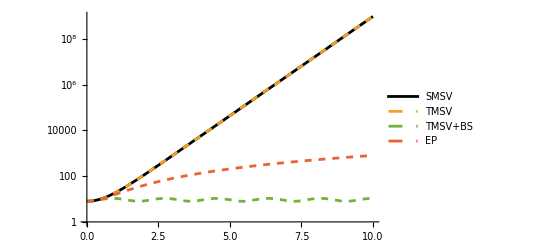

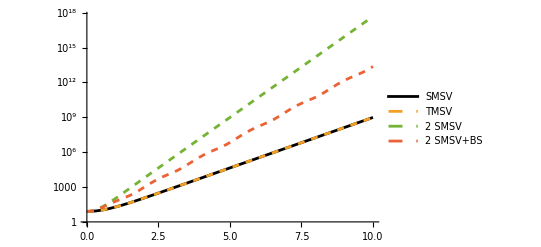

```mathematica
ω=0;ξ=1;χ=1;g=2;ξ1=1;ξ2=2;
LogPlot[{(4 (ξ^2-2 ω^2+ξ^2 Cosh[2 t √(ξ^2-ω^2)]))/(ξ^2-ω^2),8 Cosh[t χ]^2,(8 g^2-4 χ^2-4 χ^2 Cosh[2 t √(-g^2+χ^2)])/(g^2-χ^2),8+8 t^2 χ^2},{t,0,10},PlotLegends->{"SMSV","TMSV","TMSV+BS","EP"},PlotStyle->{Black,Dashed,Dashed,Dashed,Dashed}]

LogPlot[{(4 (ξ^2-2 ω^2+ξ^2 Cosh[2 t √(ξ^2-ω^2)]))/(ξ^2-ω^2),8 Cosh[t χ]^2,(2 (-2+Cosh[4 t ξ1]+Cosh[4 t ξ2]))/(-2+Cosh[2 t ξ1]+Cosh[2 t ξ2]),TSMSVBS},{t,0,10},PlotLegends->{"SMSV","TMSV","2 SMSV","2 SMSV+BS"},PlotStyle->{Black,Dashed,Dashed,Dashed,Dashed}]
```

```mathematica
Clear[g,χ]
F2ep=QFInoDisp[2,χ,χ]
F2=QFInoDisp[2,g,χ]
F3ep=QFInoDisp[3,χ,χ]
F3=QFInoDisp[3,g,χ]
```

8+8 t^2 χ^2

(8 g^2-4 χ^2-4 χ^2 Cosh[2 t √(-g^2+χ^2)])/(g^2-χ^2)

8 (1+t^2 χ^2)^2

(8 (g^2-χ^2 Cosh[√2 t √(-g^2+χ^2)])^2)/((g^2-χ^2)^2)

```mathematica
F4ep=QFInoDisp[4,χ,χ]
```

2+20 t^2 χ^2+16 t^4 χ^4+(32 t^6 χ^6)/9+(18 (9+4 t^2 χ^2))/(27+18 t^2 χ^2+4 t^4 χ^4)

```mathematica
Clear[g,χ]
F4=FnNormal[4,g,χ,t]
```

```mathematica
Clear[t,χ]
F2ep
F2
F4ep
F4
```

8+8 t^2 χ^2

(8-4 χ^2-4 χ^2 Cosh[2 t √(-1+χ^2)])/(1-χ^2)

2+20 t^2 χ^2+16 t^4 χ^4+(32 t^6 χ^6)/9+(18 (9+4 t^2 χ^2))/(27+18 t^2 χ^2+4 t^4 χ^4)

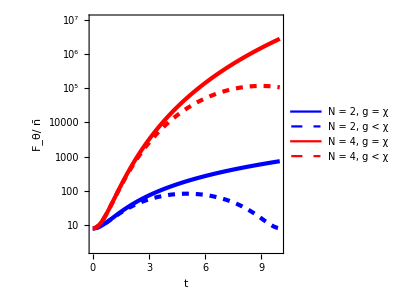

```mathematica
MapThread[Themes`AddThemeRules["LogGrid",#,GridLines->#2,Frame->True]&,{{LogPlot|ListLogPlot,LogLinearPlot|ListLogLinearPlot,LogLogPlot|ListLogLogPlot},{{Automatic,logticks},{logticks,Automatic},logticks}}];
χ=0.95;
g=1;
p=LogPlot[{F2ep,F2,F4ep,F4},{t,0,10},PlotStyle->{{Blue,Thickness[0.01]},{Blue,Dashed,Thickness[0.01]},{Red,Thickness[0.01]},{Red,Dashed,Thickness[0.01]}},GridLinesStyle->LightGray,PlotTheme->"LogGrid",GridLines->Full,FrameTicksStyle->Directive[FontSize->15],PlotRange->{2,10^7},AspectRatio->1,FrameLabel->{Style["t",18,Italic,FontFamily->"Arial"],Style[TraditionalForm["F_θ/"Overscript[n,"_"]],18,Italic,FontFamily->"Arial"]},FrameStyle->Directive[Black,Thickness[0.006]],ImageSize->300,PlotLegends->Placed[LineLegend[{Blue,{Blue,Dashed},Red,{Red,Dashed}},{"N = 2, g = χ","N = 2, g < χ","N = 4, g = χ","N = 4, g < χ"},LabelStyle->{FontSize->10},LegendMargins->{{2,2},{2,2}},Spacings->{0.4,0.3},LegendFunction->(Framed[#,Background->White,FrameStyle->Black,FrameMargins->3]&)
],{Left,Top}]
]
```

```mathematica
Clear[a,ad,x,p]
a=(x+I p)/Sqrt[2]
ad=(x-I p)/Sqrt[2]
-I/Sqrt[2](a-ad)//FullSimplify
```

(ⅈ p+x)/(√2)

(-ⅈ p+x)/(√2)

p

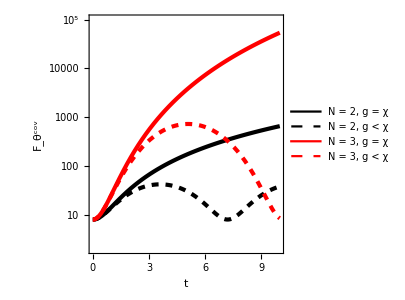

```mathematica
MapThread[Themes`AddThemeRules["LogGrid",#,GridLines->#2,Frame->True]&,{{LogPlot|ListLogPlot,LogLinearPlot|ListLogLinearPlot,LogLogPlot|ListLogLogPlot},{{Automatic,logticks},{logticks,Automatic},logticks}}];
χ=0.9;
g=1;
p=LogPlot[{F2ep,F2,F3ep,F3},{t,0,10},PlotStyle->{{Black,Thickness[0.01]},{Black,Dashed,Thickness[0.01]},{Red,Thickness[0.01]},{Red,Dashed,Thickness[0.01]}},GridLinesStyle->LightGray,PlotTheme->"LogGrid",GridLines->Full,FrameTicksStyle->Directive[FontSize->15],PlotRange->{2,10^5},AspectRatio->1,FrameLabel->{Style["t",18,Italic,FontFamily->"Arial"],Style[TraditionalForm[Superscript[Subscript[F,θ],Style["cov",FontSlant->"Plain"]]],18,Italic,FontFamily->"Arial"]},FrameStyle->Directive[Black,Thickness[0.006]],ImageSize->300,PlotLegends->Placed[LineLegend[{Black,{Black,Dashed},Red,{Red,Dashed}},{"N = 2, g = χ","N = 2, g < χ","N = 3, g = χ","N = 3, g < χ"},LabelStyle->{FontSize->10},LegendMargins->{{2,2},{2,2}},Spacings->{0.4,0.3},LegendFunction->(Framed[#,Background->White,FrameStyle->Black,FrameMargins->3]&)
],{Left,Top}]
]
```

```mathematica
Clear[g,χ]
{Fcov3,Fdisp3,n3}=QFIperPhotonEP[3]
QFIperPhotonEPAnal[3]
LeadingOrderCheck[Fcov3,Fdisp3,n3,3]
```

{16 (2+t^2 χ^2) (t χ+t^3 χ^3)^2,2 (p2^2+p3^2+x1^2+x2^2+x3^2+p1^2 (1+6 t^2 χ^2+4 t^4 χ^4)^2-8 p1 t χ (1+t^2 χ^2) (-2 p3 t χ (1+t^2 χ^2)+p2 (1+6 t^2 χ^2+4 t^4 χ^4))+4 t χ (1+t^2 χ^2) (p3^2 t χ-2 p2 (p3+2 p3 t^2 χ^2)+4 p2^2 (t χ+t^3 χ^3)+(x1+x3+2 t x2 χ+2 t^2 x3 χ^2) (t (x1+3 x3) χ+2 (x2+t^2 x2 χ^2+t^3 x3 χ^3)))),1/2 (p1^2+p2^2+p3^2+x1^2+x2^2+x3^2+4 t (-p2 (p1+p3)+x2 (x1+x3)) χ+4 t^2 (4+p2^2+p1 (p1+p3)+x2^2+x3 (x1+x3)) χ^2+8 t^3 (-p1 p2+x2 x3) χ^3+4 t^4 (2+p1^2+x3^2) χ^4)}

{16 (2+t^2 χ^2) (t χ+t^3 χ^3)^2,2 (p2^2+p3^2+x1^2+x2^2+x3^2+p1^2 (1+6 t^2 χ^2+4 t^4 χ^4)^2-8 p1 t χ (1+t^2 χ^2) (-2 p3 t χ (1+t^2 χ^2)+p2 (1+6 t^2 χ^2+4 t^4 χ^4))+4 t χ (1+t^2 χ^2) (p3^2 t χ-2 p2 (p3+2 p3 t^2 χ^2)+4 p2^2 (t χ+t^3 χ^3)+(x1+x3+2 t x2 χ+2 t^2 x3 χ^2) (t (x1+3 x3) χ+2 (x2+t^2 x2 χ^2+t^3 x3 χ^3)))),1/2 (p1^2+p2^2+p3^2+x1^2+x2^2+x3^2+4 t (-p2 (p1+p3)+x2 (x1+x3)) χ+4 t^2 (4+p2^2+p1 (p1+p3)+x2^2+x3 (x1+x3)) χ^2+8 t^3 (-p1 p2+x2 x3) χ^3+4 t^4 (2+p1^2+x3^2) χ^4)}

leading order covariant 16 χ^8

True

leading order displacement 32 (p1^2+x3^2) χ^8

True

leading order mean photon number  2 (2+p1^2+x3^2) χ^4

True

```mathematica
Clear[g,χ]
{Fcov4,Fdisp4,n4}=QFIperPhotonEPAnal[4]
LeadingOrderCheck[Fcov4,Fdisp4,n4,4]
```

{48 t^2 χ^2+16/81 t^4 χ^4 (729+900 t^2 χ^2+522 t^4 χ^4+144 t^6 χ^6+16 t^8 χ^8),2/81 (81 (p1^2+p2^2+p3^2+p4^2+x1^2+x2^2+x3^2+x4^2)-648 t (p1 p2+p3 (p2+p4)-x1 x2-x3 (x2+x4)) χ+324 t^2 (3 p1^2+4 p1 p3+4 p3^2+(2 p2+p4)^2+4 x2^2+(x1+2 x3)^2+4 x2 x4+3 x4^2) χ^2-216 t^3 (21 p1 p2+24 p2 p3+8 p1 p4+9 p3 p4-9 x1 x2-24 x2 x3-8 x1 x4-21 x3 x4) χ^3+108 t^4 (45 p2^2+3 (p1+p3) (11 p1+9 p3)+28 p2 p4+3 p4^2+3 x1^2+28 x1 x3+45 x3^2+3 (x2+x4) (9 x2+11 x4)) χ^4-432 t^5 (4 p3 (5 p2+p4)+p1 (26 p2+7 p4)-4 x2 (x1+5 x3)-(7 x1+26 x3) x4) χ^5+144 t^6 (42 p2^2+3 (p1+p3) (14 p1+5 p3)+15 p2 p4+p4^2+x1^2+15 x1 x3+42 x3^2+3 (x2+x4) (5 x2+14 x4)) χ^6-576 t^7 (19 p1 p2+9 p2 p3+3 p1 p4+p3 p4-x1 x2-9 x2 x3-3 x1 x4-19 x3 x4) χ^7+144 t^8 (33 p1^2+21 p2^2+28 p1 p3+4 p3^2+4 p2 p4+4 x2^2+4 x1 x3+21 x3^2+28 x2 x4+33 x4^2) χ^8-384 t^9 (3 p2 (4 p1+p3)+p1 p4-x1 x4-3 x3 (x2+4 x4)) χ^9+192 t^10 (9 p1^2+4 p1 p3+3 (p2^2+x3^2)+4 x2 x4+9 x4^2) χ^10+768 t^11 (-p1 p2+x3 x4) χ^11+256 t^12 (p1^2+x4^2) χ^12),1/2 (p1^2+p2^2+p3^2+p4^2+x1^2+x2^2+x3^2+x4^2)-2 t (p1 p2+p3 (p2+p4)-x1 x2-x3 (x2+x4)) χ+2 t^2 (6+p1^2+p1 p3+p3^2+p2 (p2+p4)+x2^2+x3 (x1+x3)+x2 x4+x4^2) χ^2-4/3 t^3 (3 p2 (p1+p3)+p1 p4-x1 x4-3 x3 (x2+x4)) χ^3+2/3 t^4 (3 p1^2+4 p1 p3+3 (4+p2^2+x3^2)+4 x2 x4+3 x4^2) χ^4+8/3 t^5 (-p1 p2+x3 x4) χ^5+8/9 t^6 (2+p1^2+x4^2) χ^6}

leading order covariant (256 χ^12)/81

True

leading order displacement 512/81 (p1^2+x4^2) χ^12

True

leading order mean photon number  8/9 (2+p1^2+x4^2) χ^6

True

```mathematica
Clear[g,χ,t]
{Fcov5,Fdisp5,n5}=QFIperPhotonEPAnal[5]
LeadingOrderCheck[Fcov5,Fdisp5,n5,5]
```

{16/81 t^2 χ^2 (3+t^2 χ^2) (108+315 t^2 χ^2+t^4 χ^4 (387+237 t^2 χ^2+77 t^4 χ^4+13 t^6 χ^6+t^8 χ^8)),0,4/9 t^2 χ^2 (36+27 t^2 χ^2+8 t^4 χ^4+t^6 χ^6)}

leading order covariant (16 χ^16)/81

True

leading order displacement 0

True

leading order mean photon number  (4 χ^8)/9

True

```mathematica
x1=0;x2=0;x3=0;x4=0;x5=0;p1=0;p2=0;p3=0;p4=0;p5=0;x6=0;p6=0;
Clear[g,χ,t]
{Fcov6,Fdisp6,n6}=QFIperPhotonEPAnal[6]
LeadingOrderCheck[Fcov6,Fdisp6,n6,6]
```

{80 t^2 χ^2+272 t^4 χ^4+(32 t^6 χ^6 (641250+523125 t^2 χ^2+261450 t^4 χ^4+t^6 χ^6 (84300+17800 t^2 χ^2+2425 t^4 χ^4+200 t^6 χ^6+8 t^8 χ^8)))/50625,0,4/225 t^2 χ^2 (1125+900 t^2 χ^2+300 t^4 χ^4+50 t^6 χ^6+4 t^8 χ^8)}

leading order covariant (256 χ^20)/50625

True

leading order displacement 0

True

leading order mean photon number  (16 χ^10)/225

True

```mathematica
x1=0;x2=0;x3=0;x4=0;x5=0;p1=0;p2=0;p3=0;p4=0;p5=0;x6=0;p6=0;x7=0;p7=0;
Clear[g,χ,t]
{Fcov7,Fdisp7,n7}=QFIperPhotonEPAnal[7]
LeadingOrderCheck[Fcov7,Fdisp7,n7,7]
```

{96 t^2 χ^2+336 t^4 χ^4+(4672 t^6 χ^6)/9+(4000 t^8 χ^8)/9+(16 t^10 χ^10 (61017300+21951000 t^2 χ^2+5508000 t^4 χ^4+978075 t^6 χ^6+16 t^8 χ^8 (7650+657 t^2 χ^2+36 t^4 χ^4+t^6 χ^6)))/4100625,0,24 t^2 χ^2+(4 t^4 χ^4 (10125+3600 t^2 χ^2+675 t^4 χ^4+72 t^6 χ^6+4 t^8 χ^8))/2025}

leading order covariant (256 χ^24)/4100625

True

leading order displacement 0

True

leading order mean photon number  (16 χ^12)/2025

True

```mathematica
x1=0;x2=0;x3=0;x4=0;x5=0;p1=0;p2=0;p3=0;p4=0;p5=0;x6=0;p6=0;x7=0;p7=0;x8=0;p8=0;
Clear[g,χ,t]
{Fcov8,Fdisp8,n8}=QFIperPhotonEPAnal[8]
LeadingOrderCheck[Fcov8,Fdisp8,n8,8]
```

{112 t^2 χ^2+400 t^4 χ^4+(5696 t^6 χ^6)/9+(5024 t^8 χ^8)/9+1/9845600625 64 t^10 χ^10 (47827739925+18154801350 t^2 χ^2+4931879400 t^4 χ^4+987189525 t^6 χ^6+4 t^8 χ^8 (36900675+t^2 χ^2 (4124673+340452 t^2 χ^2+20090 t^4 χ^4+784 t^6 χ^6+16 t^8 χ^8))),0,28 t^2 χ^2+24 t^4 χ^4+(80 t^6 χ^6)/9+(16 t^8 χ^8)/9+(16 t^10 χ^10)/75+(32 t^12 χ^12)/2025+(64 t^14 χ^14)/99225}

leading order covariant (4096 χ^28)/9845600625

True

leading order displacement 0

True

leading order mean photon number  (64 χ^14)/99225

True

```mathematica
x1=0;x2=0;x3=0;x4=0;x5=0;p1=0;p2=0;p3=0;p4=0;p5=0;x6=0;p6=0;x7=0;p7=0;x8=0;p8=0;x9=0;p9=0;
Clear[g,χ,t]
{Fcov9,Fdisp9,n9}=QFIperPhotonEPAnal[9]
LeadingOrderCheck[Fcov9,Fdisp9,n9,9]
```

{128 t^2 χ^2+464 t^4 χ^4+(2240 t^6 χ^6)/3+672 t^8 χ^8+(86336 t^10 χ^10)/225+(101504 t^12 χ^12)/675+(4229632 t^14 χ^14)/99225+(16 t^16 χ^16 (5574460500+909033300 t^2 χ^2+115190964 t^4 χ^4+11381328 t^6 χ^6+t^8 χ^8 (872004+50960 t^2 χ^2+2192 t^4 χ^4+64 t^6 χ^6+t^8 χ^8)))/9845600625,0,32 t^2 χ^2+28 t^4 χ^4+(32 t^6 χ^6)/3+(4 t^8 χ^8 (55125+7056 t^2 χ^2+588 t^4 χ^4+32 t^6 χ^6+t^8 χ^8))/99225}

leading order covariant (16 χ^32)/9845600625

True

leading order displacement 0

True

leading order mean photon number  (4 χ^16)/99225

True

```mathematica
x1=0;x2=0;x3=0;x4=0;x5=0;p1=0;p2=0;p3=0;p4=0;p5=0;x6=0;p6=0;x7=0;p7=0;x8=0;p8=0;x9=0;p9=0;x10=0;p10=0;
Clear[g,χ,t]
{Fcov10,Fdisp10,n10}=QFIperPhotonEPAnal[10]
LeadingOrderCheck[Fcov10,Fdisp10,n10,10]
```

$Aborted

leading order covariant (256 χ^36)/64596985700625

χ==0

leading order displacement 0

True

leading order mean photon number  (16 χ^18)/8037225

χ==0

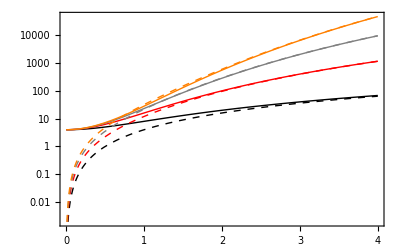

```mathematica
χ=1;
x1=0;x2=0;x3=0;x4=0;x5=0;p1=0;p2=0;p3=0;p4=0;p5=0;x6=0;p6=0;
p=LogPlot[{Fcov2/n2,Fcov3/n3,Fcov4/n4,Fcov5/n5, n2, n3, n4, n5},{t,0,4},PlotStyle->{Black,Red,Gray,Orange,{Black,Dashed},{Red,Dashed},{Gray,Dashed},{Orange,Dashed}},GridLinesStyle->LightGray,PlotTheme->"LogGrid",GridLines->Full]
```